## Examples used during the lectures

## Day 1

### Demographic model and invasion fitness example

```mathematica
Clear["Global`*"]
```

#### demographics in monomorphic pop

```mathematica
(* demographics in monomorphic pop *)
```

```mathematica
Nt1 ==( s + f[x]/(1+γ Nt)) Nt ;
soln = Flatten@Solve[ ( s + f[x]/(1+γ Nt))  ==1, Nt]
```

{Nt→(1-s-f[x])/((-1+s) γ)}

```mathematica
Nt == 1/γ(f[x]/(1-s)-1) /. soln //Simplify
```

True

#### invasion fitness example

```mathematica
s + f[y]/(1+γ Nt)  /.  soln  //Simplify ;
% ==  s + (1-s) f[y]/f[x] //Simplify
```

True

### Asocial model

```mathematica
Clear["Global`*"]
```

```mathematica
f = fmax Exp[-y^2/(2 σg^2)] ; 
w = f/(f /. y-> x)  ;
```

```mathematica
S = D[w,y] /. y-> x
```

-x/σg^2

```mathematica
sing = Flatten@Solve[S ==0,x]
```

{x→0}

```mathematica
J = D[S,x] /.sing
```

-1/σg^2

```mathematica
H = D[w,y,y] /. y-> x   ;
%  /.sing
```

-1/σg^2

```mathematica
D[w,x,y] /. y-> x  /.sing
```

0

### Social model

```mathematica
Clear["Global`*"]
```

Wright - Fisher model in large population where fecundity is determined by the amount of resources obtained under trait matching competition where resources are Normaly distributed

```mathematica
(* Integrate[Exp[-(y-θ)^2/(2 σg^2)]/(n Exp[-(x-θ)^2/(2 σg^2)])PDF[NormalDistribution[0,σr],θ],{θ,-∞,∞}]  ; 
Assuming[σr>0,Simplify[%]] *)
```

```mathematica
PDF[NormalDistribution[0,σr],θ]
```

(ⅇ^(-θ^2/(2 σr^2)))/(√(2 π) σr)

```mathematica
(ⅇ^(((x-y) ((x+y) σg^2+(x-y) σr^2))/(2 σg^4)))/n == 1/n ⅇ^((x^2-y^2 +(x-y)^2 σr^2/σg^2)/(2 σg^2))//Simplify
```

True

```mathematica
R =1/n ⅇ^(((x^2-y^2) +(x-y)^2 σr^2/σg^2)/(2 σg^2)) ; 
f = n R ; 
w = f
```

ⅇ^((x^2-y^2+((x-y)^2 σr^2)/σg^2)/(2 σg^2))

```mathematica
D[w,y]
```

(ⅇ^((x^2-y^2+((x-y)^2 σr^2)/σg^2)/(2 σg^2)) (-2 y-(2 (x-y) σr^2)/σg^2))/(2 σg^2)

```mathematica
S = D[w,y] /. y-> x
```

-x/σg^2

```mathematica
sing = Flatten@Solve[S ==0,x]
```

{x→0}

```mathematica
J = D[S,x] /.sing
```

-1/σg^2

```mathematica
H = D[w,y,y] /. y-> x  ;
%  /.sing //Simplify  ;
% ==1/σg^4 (σr^2-σg^2 )
```

True

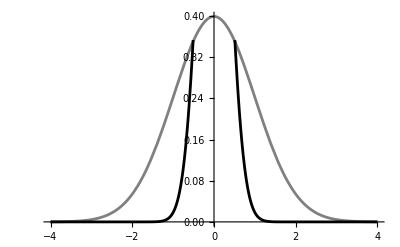

```mathematica
p1 = Plot[PDF[NormalDistribution[0,σr],θ]/. σr-> 1 ,{θ,-4,4} ,PlotStyle->Gray] ;
p2 = Plot[Exp[-(y/(2 σg^2))^2] /. σg-> 0.5 ,{y,-4,4} ,PlotStyle->Black ] ;
Show[p1,p2]
```

### Social and survival model -- with evolutionary suicide

```mathematica
Clear["Global`*"]
```

Survival with model in large population where fecundity is determined by fecundity

```mathematica
w = s + f[y,x]/(1+γ n[x]) ;
soln = Flatten@Solve[w ==1/.y->x, n[x]]
```

{n[x]→(1-s-f[x,x])/((-1+s) γ)}

```mathematica
n[x] == 1/γ(f[x,x]/(1-s)-1) /. soln //Simplify
```

True

```mathematica
w = s + f[y,x]/(1+γ n[x]) ;
w =w/.soln  //Simplify  ;
% == s + (1-s) f[y,x]/f[x,x] //Simplify
```

True

```mathematica
f[y_,x_] :=  R[x] y/x Exp[-y^2/(2 σ^2)] ; 
(* where R[x] is the equilibrium amount of resources in a x population and y/x is the amount of resources a y mutant gets *)
```

```mathematica
S = D[w,y] /. y-> x  //Simplify
```

((-1+s) (x^2-σ^2))/(x σ^2)

```mathematica
sing =Solve[S==0,x]
```

{{x→-σ},{x→σ}}

```mathematica
sing = sing[[2]] ;
```

```mathematica
J = D[S,x] /.sing  //FullSimplify
```

(2 (-1+s))/σ^2

```mathematica
H = D[w,y,y]  /. y-> x   //FullSimplify;
%  /.sing
```

(2 (-1+s))/σ^2

```mathematica
(* observe that selection is independent of resource levels. What if those decline with the trait ? e.g. due to interference as predation decreases birth rate ?   *)
```

#### with resource birth rate declining with consumer trait in density independent way

```mathematica
(d R)/dt == ( b(1-x) - d R ) R ;    
Solve[ ( b(1-x) - d R ) R  == 0 ,R ] /. b -> r0 d  //Simplify
```

{{R→0},{R→r0-r0 x}}

```mathematica
1/γ(f[x,x]/(1-s)-1)   /.R -> Function[x,r0(1-x) ] /. soln /.sing  //Simplify  ; 

% ==1/γ ((r0 (1-σ))/(√ⅇ (1-s))-1 )//Simplify
```

True

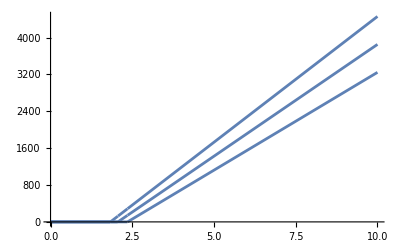

```mathematica
Plot[Evaluate[Clip[(-1+(r0 (-1+σ))/(√ⅇ (-1+s)))/γ/. γ->.001 /.s->0/.σ-> {0.1,0.2,0.3},{0,∞}]],{r0,0,10},AxesOrigin->{0,0}]
```

#### with resource birth rate declining with consumer trait in density dependent way

```mathematica
(d R)/dt == ( b(1-x)n[x] - d R ) R ;    
Solve[ ( b(1-x)n[x] - d R ) R  == 0 ,R ]/. b -> r0 d  //Simplify
```

{{R→0},{R→-r0 (-1+x) n[x]}}

```mathematica
soln
```

{n[x]→(1-s-ⅇ^(-x^2/(2 σ^2)) R[x])/((-1+s) γ)}

```mathematica
Solve[{R[x]== -r0 (-1+x) n[x],n[x] == (1-s-ⅇ^(-x^2) R[x])/((-1+s) γ)},{R[x],n[x]}] //FullSimplify
```

{{R[x]→1/(-(ⅇ^(-x^2))/(-1+s)+γ/(r0 (-1+x))),n[x]→1/((ⅇ^(-x^2) r0 (-1+x))/(-1+s)-γ)}}

```mathematica
1/γ(f[x,x]/(1-s)-1)   /.R -> Function[x,1/(-(ⅇ^(-x^2))/(-1+s)+γ/(r0 (-1+x))) ] /. soln /.sing  //Simplify
```

(-1+(ⅇ^(-1/2+σ^2) (r0-r0 σ))/(r0+ⅇ^(σ^2) (-1+s) γ-r0 σ))/γ

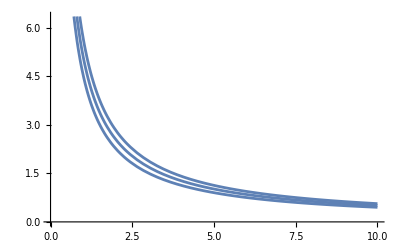

```mathematica
Plot[Evaluate[Clip[-(2 √ⅇ (-1+s))/(-((-2+√2) r0)+2 √ⅇ (-1+s) γ)/. γ->.001 /.s-> {0,0.1,0.2},{0,∞}]],{r0,0,10},AxesOrigin->{0,0}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
D[w[x,x,n[x]],x]
```

n'[x] w^(0,0,1)[x,x,n[x]]+w^(0,1,0)[x,x,n[x]]+w^(1,0,0)[x,x,n[x]]

```mathematica
n'[x] == - (Derivative[0,1,0][w][x,x,n[x]]+Derivative[1,0,0][w][x,x,n[x]])/(Derivative[0,0,1][w][x,x,n[x]])
```

n'[x]==-(w^(0,1,0)[x,x,n[x]]+w^(1,0,0)[x,x,n[x]])/(w^(0,0,1)[x,x,n[x]])

```mathematica
n'[x] ==  (Derivative[0,1,0][w][x,x,n[x]])/(- Derivative[0,0,1][w][x,x,n[x]])
```

n'[x]==-(w^(0,1,0)[x,x,n[x]])/(w^(0,0,1)[x,x,n[x]])